# Analytical solutions for simple cases

First let us assume is small i.e.,  
and using geometric series expansion . 
We also assume that 
 
as a quadratic geometry. Thus the resulting ODE is:

The ODE is of the form: 
where 
 
.
The solution is

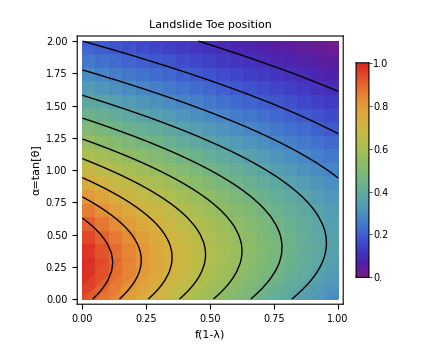

/Users/mallick/Documents/GitHub/landslides/analyticsol/LandslideToeParameterPlot.jpg

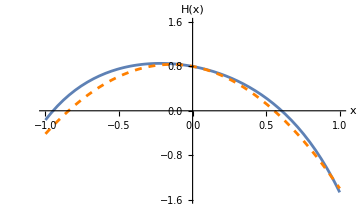
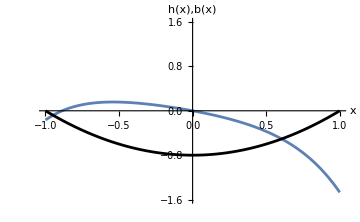

```mathematica
(*Define parameters as symbolic*)
ClearAll[H,H0,x,α](*α -> Tan[θ]*)
P[x_]:=Subscript[b, 0] (α-2 Subscript[b, 0] x (1+α^2))
Q[x_]:=-Subscript[f, λ]+α-4 Subscript[b, 0] x (1+α^2)
(*Solve the ODE symbolically*)
solH=DSolve[{H'[x]+P[x] H[x]==Q[x],H[0]==H0},H[x],{x,-1,1}];
Hanalytical = H[x]/.solH[[1]];

(*Define H[x]*)
HBC = 0.8;
bmax=HBC;
αplot = 0.3;
fplot=0.6;
Happroxfun[x_,fv_?NumericQ,αv_?NumericQ]:=HBC+(αv-(fv+bmax*HBC*αv))*x+(bmax*x^2)/2*(fv*αv-(4+5*αv^2));
Hfun[x_,fv_,αv_]:=Evaluate[Hanalytical/.{x->x,Subscript[f, λ]->fv,α->αv,Subscript[b, 0]->bmax,H0->HBC}];

(*Function to return positive root or 1 if none exists*)
xPosRoot[fv_?NumericQ,αv_?NumericQ]:=Module[{roots},roots=x/. NSolve[Hfun[x,fv,αv]==0&&0<=x<=1,x,Reals];
If[roots==={}||!VectorQ[roots,NumericQ],1,Min[roots]]];

dplot=DensityPlot[xPosRoot[fv,αv],{fv,0,1},{αv,0,2},ColorFunction->ColorData[{"Rainbow",{0,1}}],FrameLabel->{"f(1-λ)","α=tan[θ]"},PlotLabel->"Landslide Toe position",PlotPoints->20,Mesh->False,PlotLegends->BarLegend[{"Rainbow",{0,1}}],ImageSize->Medium,LabelStyle->{FontSize->15}
];
cplot = ContourPlot[xPosRoot[fv,αv],{fv,0,1},{αv,0,2},Contours->10,ContourStyle->Black,ContourShading->None
];
fig=Show[dplot,cplot]
(*Export[NotebookDirectory[]<>"LandslideToeParameterPlot.jpg",fig,"JPEG"]*)
(*Plot one H-x profile*)
Row[{
Plot[{Hfun[x,fplot,αplot],Happroxfun[x,fplot,αplot]},{x,-1,1},PlotRange->{-2*bmax,2*HBC},AxesLabel->{"x","H(x)"},LabelStyle->{FontSize->13},PlotStyle->{DarkBlue,{Orange,Dashed}},ImageSize->Medium],
Spacer[20],
Plot[{Hfun[x,fplot,αplot]+bmax*(x^2-1),bmax*(x^2-1)},{x,-1,1},PlotRange->{-2*bmax,2*HBC},AxesLabel->{"x","h(x),b(x)"},LabelStyle->{FontSize->13},PlotStyle->{DarkBlue,Black},ImageSize->Medium]
}]
```

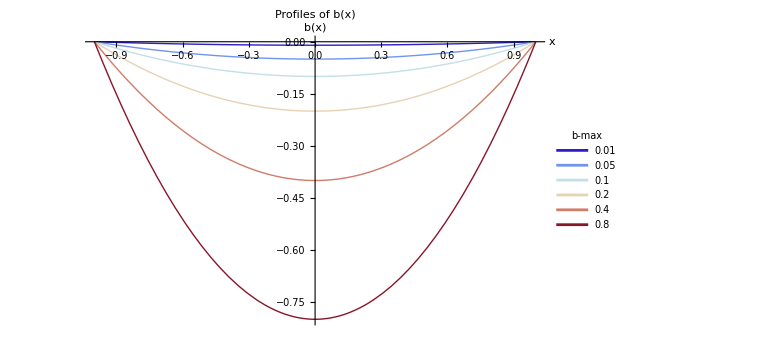

```mathematica
bmaxList={0.01,0.05,0.1,0.2,0.4,0.8};
colorMap=ColorData["ThermometerColors"];  (*Or "Rainbow","Viridis",etc.*)
colors=colorMap/@Rescale[Range[Length[bmaxList]]];  (*Evenly spaced colors*)
Plot[Evaluate@Table[bmax*(x^2-1),{bmax,bmaxList}],{x,-1,1},PlotStyle->(Directive[#,Thick]&/@colors),PlotLegends->Placed[LineLegend[Style[#,FontSize->12]&/@ToString/@bmaxList,LegendLabel->Style["b-max",FontSize->14]],Right],AxesLabel->{"x","b(x)"},LabelStyle->{FontSize->14},PlotLabel->Style["Profiles of b(x)",FontSize->16],ImageSize->Large]
```